```mathematica
f[x_] := x^2/10 - 2*Sin[x];
```

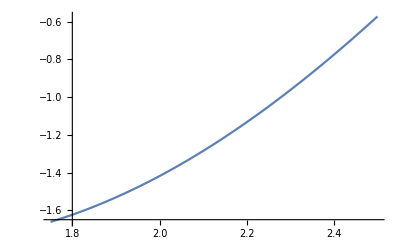

```mathematica
Plot[f[x],{x,1.75,2.5}]
```

```mathematica
interpol:=Module[{},
x1=0;
x2=1;
x3=4;
x4s={};
For[i=0,i< 7,
f2=f[x2];
f3=f[x3];
x4=x2-1/2*(((x2-x1)^2*(f2-f3)-(x2-x3)^2*(f2-f[x1]))/((x2-x1)*(f2-f3)-(x2-x3)*(f2-f[x1])));
AppendTo[x4s,x4//N];
If[f[x4]<f2,x3=x4,x1=x4 ];
i++;

];
{x4s,x4//N}
]
```

```mathematica
interpol
```

{{1.50553,1.48094,1.48616,1.48504,1.48528,1.48523,1.48524},1.48524}